# Maximum Likelihood Inference of s and h from trios

## We define the average fitness of genotypes arising from all three informative couples (AA x Aa, Aa x Aa, Aa x aa):

```mathematica
w1[s_,h_]:=(2+h*s )/2; (* AA x Aa *)
```

```mathematica
w2[s_,h_]:=(4+2*h*s+s)/4; (* Aa x Aa *)
```

```mathematica
w3[s_,h_]:=(2+h*s+s)/2;(* Aa x aa *)
```

## Now we introduce the likelihood function where:

### a is the count of AA born from AA x Aa parents;

### b is the count of Aa born from AA x Aa parents;

### c is the count of AA born from Aa x Aa parents;

### d is the count of Aa born from Aa x Aa parents;

### e is the count of aa born from Aa x Aa parents;

### f is the count of Aa born from Aa x aa parents;

### g is the count of aa born from Aa x aa parents;

## The likelihood function (assuming independence among trios, offspring, and sites):

```mathematica
FullLik[s_,h_]:= Multinomial[a,b,c,d,e,f,g]*((1/(2*w1[s,h]))^c1)*(((1+h*s)/(2*w1[s,h]))^c2)*((1/(4*w2[s,h]))^c3)*(((1+h*s)/(2*w2[s,h]))^c4)*(((1+s)/(4*w2[s,h]))^c5)*(((1+h*s)/(2*w3[s,h]))^c6)*(((1+s)/(2*w3[s,h]))^c7)
```

```mathematica
Lik[s_,h_]:= ((1/(2*w1[s,h]))^c1)*(((1+h*s)/(2*w1[s,h]))^c2)*((1/(4*w2[s,h]))^c3)*(((1+h*s)/(2*w2[s,h]))^c4)*(((1+s)/(4*w2[s,h]))^c5)*(((1+h*s)/(2*w3[s,h]))^c6)*(((1+s)/(2*w3[s,h]))^c7)
```

```mathematica
LogLik=Log[FullLik[s,h]]
```

```mathematica
Dist:=ProbabilityDistribution[FullLik[s,h], {s,-Infinity, 0}, {h,-1,1 }]
```

```mathematica
Integrate[FullLik[s, h],{s,-Infinity, 0}, {h,-1,1 }, Assumptions->c1=100,c2=100,c3=50,c4=100,c5=50,c6=100,c7=100]
```

```mathematica
(*https://community.wolfram.com/groups/-/m/t/160450*)
```

```mathematica
(*NSolve[{PDS==0,PDH==0},{s,h},Reals]*)
```

## The partial derivatives:PDS=D[Lik[s,h],s]

```mathematica
PDH=D[FullLik[s,h],h]
```

```mathematica
PDS=D[FullLik[s,h],s]
```

```mathematica
(*Solve[{PDS==0,PDH==0},{s,h},Reals]*)
```

We take an specific values of a-g from an example dataset

```mathematica
c1=100
c2=100
c3=50
c4=100
c5=50
c6=100
c7=100
```

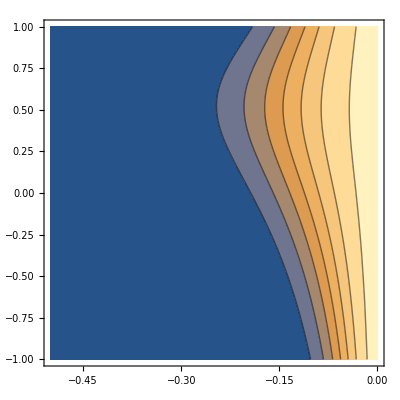

```mathematica
ContourPlot[FullLik[s,h],{s,0,-0.5},{h,-1,1}]
```

```mathematica
(*Solve[PDS==0,s,h=0]*)
```

```mathematica
(*Solve[PDH==0,h,s=0]*)
```